```mathematica
NN = 3;



m0[m_] := m

m1[m_] := m ⅇ^(2 π ⅈ / NN)

m2[m_] := m ⅇ^(4 π ⅈ / NN)

σ0[m_] := ⅇ^(1/NN Log[ 1 + m^NN])Piecewise[  {{  ⅇ^(2 π ⅈ / NN),Arg[m] ≥ π /3 } , { ⅇ^(-2 π ⅈ / NN),  Arg[m] ≤ - π /3}}, 1 ]

σ1[m_] := σ0[m] ⅇ^(2 π ⅈ / NN)


σ2[m_] := σ0[m] ⅇ^(4 π ⅈ / NN)

W0[m_] :=  (- 1)/(2π)( NN σ0[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ0[m] - m ⅇ^(2 π ⅈ  j/ NN)])

W1[m_] :=  (- 1)/(2π)( NN σ1[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ1[m] - m ⅇ^(2 π ⅈ  j/ NN)])

W2[m_] :=  (- 1)/(2π)( NN σ2[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ2[m] - m ⅇ^(2π ⅈ  j/ NN)])

M10[m_] := W1[m]  -  W0[m]

M21[m_] := W2[m]  -  W1[m]

M02[m_] := W0[m]  -  W2[m]

Q10[m_]  := ⅈ ( m1[m]  -  m0[m] )

Q21[m_]  := ⅈ ( m2[m]  -  m1[m] )

Q02[m_]  := ⅈ ( m0[m]  -  m2[m] )


M10u[m_] :=   ( ⅇ^(- 2 π ⅈ /3)  -  ⅇ^(2 π ⅈ /3) ) W2[m]    +    ⅈ m0[m]

M21u[m_] := ⅇ^(2 π ⅈ /3) M10u[m]

M02u[m_]  := ⅇ^(2 π ⅈ /3) M21u[m]


M10l[m_] :=  (  1  -  ⅇ^(- 2 π ⅈ /3)  ) W1[m]     +     ⅈ m1[m]

M21l[m_] :=  ⅇ^(2 π ⅈ /3) M10l[m]

M02l[m_] :=  ⅇ^(2 π ⅈ /3) M21l[m]

D10u[m_, n_]  := M10u[m]   +   n Q10[m]

D21u[m_, n_]  := ⅇ^(2 π ⅈ /3) D10u[m, n]

D02u[m_, n_]  := ⅇ^(2 π ⅈ / 3)D21u[m, n]


D10l[m_, n_]  := M10l[m]   +   n Q10[m]

D21l[m_, n_]  := ⅇ^(2 π ⅈ /3) D10l[m, n]

D02l[m_, n_]  := ⅇ^(2 π ⅈ / 3)D21l[m, n]


mru[a_, b_]  :=  ⅇ^(+ 2 π ⅈ /3)  ⅇ^(ⅈ 1/3 Arg[ a  +  ⅈ b ])  √(a^2 + b^2)

mrl[a_, b_]  :=  ⅇ^(- 2 π ⅈ /3)  ⅇ^(ⅈ 1/3 Arg[ a  +  ⅈ b ])  √(a^2 + b^2)


z    [a_, b_]  :=  a   +  ⅈ b
```

```mathematica
mrr[a_, b_]  :=  ⅇ^(ⅈ 1/3 Arg[ a  +  ⅈ b ])  √(a^2 + b^2)

mrc[a_, b_]  :=  ⅇ^(ⅈ 1/3 Arg[ a  +  ⅈ b ])  (  a^2  +  b^2  )^(1/6)


Q20[m_]  := ⅈ ( m2[m]  -  m0[m] )


MM10r[m_] :=   (  ⅇ^(2 π ⅈ / 3)  -  1  )W0[m]    +    ⅈ m2[m]

MM21r[m_] := ⅇ^(2 π ⅈ /3) MM10r[m]

MM02r[m_]  := ⅇ^(2 π ⅈ /3) MM21r[m]

DD10r[m_, n_]  := MM10r[m]   +   n Q10[m]

DD21r[m_, n_]  := ⅇ^(2 π ⅈ /3) DD10r[m, n]

DD02r[m_, n_]  := ⅇ^(2 π ⅈ / 3)DD21r[m, n]
```

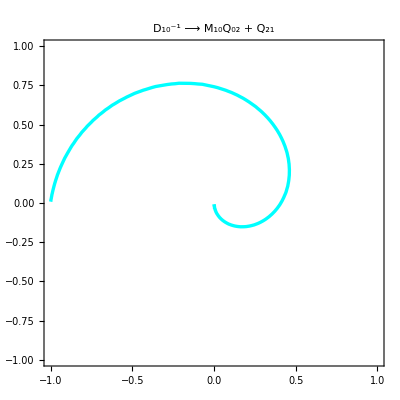

```mathematica
distance =1.0;
ContourPlot[   Evaluate[     {   Im[   (MM10r[  mrr[x, y]  ]    +    Q02[  mrr[x, y]  ])/Q21[  mrr[x, y]  ]  ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ]  },
		         PlotLabel->Style[   "D_10^-1  ⟶  M_10Q_02  +  Q_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

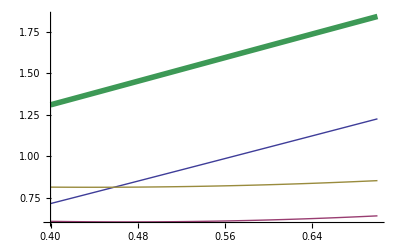

```mathematica
b  =  0.1;
Plot[  {  Abs[  Q21[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ],
		Abs[  DD10r[  z[a, b],  -1  ]  ]  },
	{  a,  0.4, 0.7  },
	PlotStyle-> {  Thick,  Thick,  Thick,  Thickness[0.01]  }  ]
```

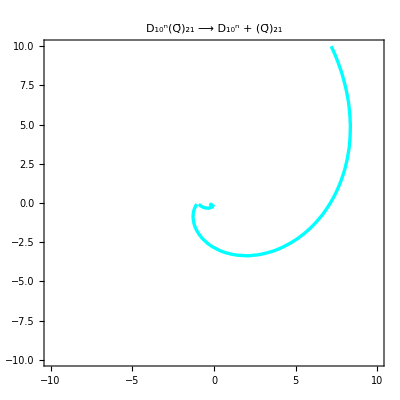

```mathematica
distance =10.0;
n  =  0;
spiral1 =
ContourPlot[   Evaluate[     {   Im[   (DD10r[  mrr[x, y],  n  ]    -    Q21[  mrr[x, y]  ])/(-  Q21[  mrr[x, y]  ])  ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D_10^n(Q̄)_21  ⟶  D_10^n  +  (Q̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

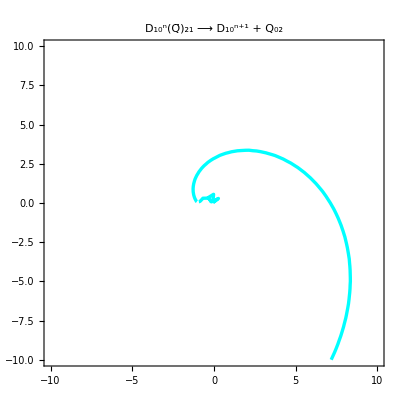

```mathematica
distance =10.0;
n  =  -1;
spiralm1 =
ContourPlot[   Evaluate[     {   Im[   DD10r[  mrr[x, y],  n   +  1 ]/Q02[  mrr[x, y]  ]  ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D_10^n(Q̄)_21  ⟶  D_10^(n+1)  +  Q_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

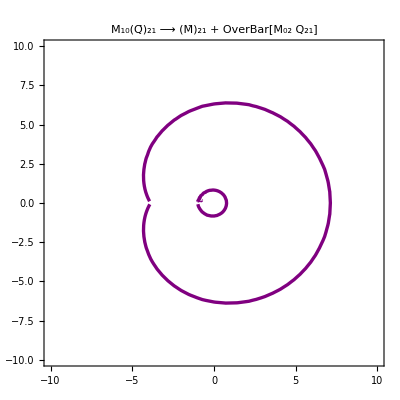

```mathematica
distance=10;
double = 
ContourPlot[   Evaluate[     {   Im[   (- MM21r[  mrr[x,y]  ])/(- (  MM02r[  mrr[x,y]  ]  +  Q21[  mrr[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Purple ] },
		         PlotLabel->Style[   "M_10(Q̄)_21  ⟶  (M̄)_21  +  OverBar[M_02 Q_21]",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

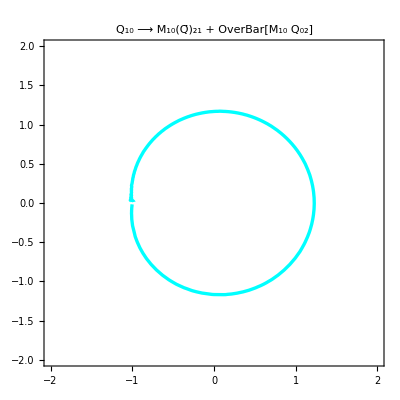

```mathematica
distance=2;
quark = 
ContourPlot[   Evaluate[     {   Im[   (MM10r[  mrr[x,y]  ]  -  Q21[  mrr[x, y]  ])/(- (  MM10r[  mrr[x,y]  ]  +  Q02[  mrr[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "Q_10  ⟶  M_10(Q̄)_21  +  OverBar[M_10 Q_02]",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

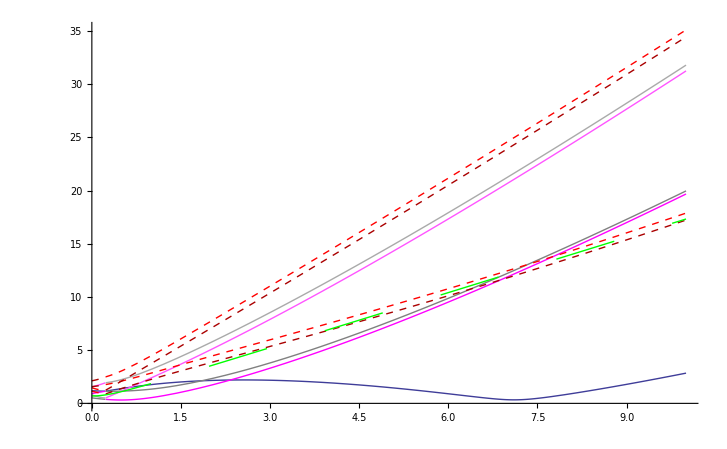

```mathematica
b = 0.4;
Plot[  {  Abs[  MM10r[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ],  
	Abs[  DD10r[  z[a, b],  -2  ]  -  Q21[  z[a, b]  ]  ],  Abs[  DD10r[  z[a, b],  1  ]  -  Q21[  z[a, b]  ]  ], 
	Abs[  DD10r[  z[a, b],  -1  ]   ],  Abs[  DD10r[  z[a, b],  1  ]   ],
	Abs[  DD10r[  z[a, b],  -2  ]   ],  Abs[  DD10r[  z[a, b],  2  ]   ],
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 10 },  
	PlotStyle->{  Thick, Directive[Magenta,Thick], Directive[Gray, Thick],
				Directive[Lighter[Magenta], Thick],  Directive[Lighter[Gray], Thick],
				Directive[  Darker[Red], Dashed ],  Directive[Red,  Dashed  ],
				Directive[  Darker[Red], Thick, Dashed ],  Directive[ Red,  Thick, Dashed  ],
				Directive[  Green, Dashing[0.06], Thick  ]  }  ]
```

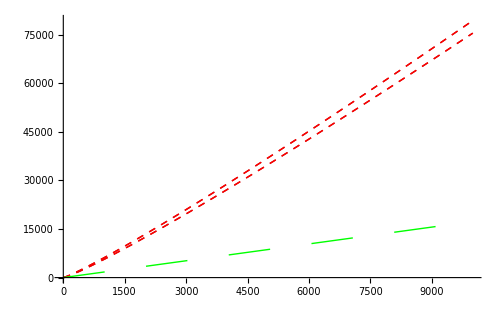

```mathematica
b = 0.4;
Plot[  {  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ],  
	Abs[  DD10r[  z[a, b],  -2  ]  -  Q21[  z[a, b]  ]  ],  Abs[  DD10r[  z[a, b],  1  ]  -  Q21[  z[a, b]  ]  ], 
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 10000 },  
	PlotStyle->{  Directive[  Darker[Red], Dashed ],  Directive[Red,  Dashed  ],
				Directive[  Darker[Red], Thick, Dashed ],  Directive[ Red,  Thick, Dashed  ],
				Directive[  Green, Dashing[0.06], Thick  ]  }  ]
```

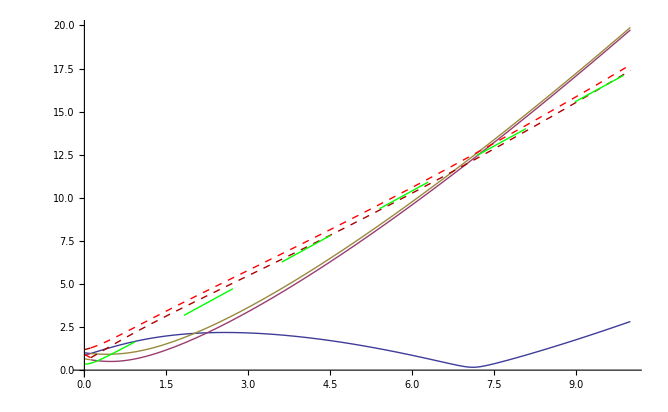

```mathematica
b = 0.2;
Plot[  {  Abs[  MM10r[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ],  
	Abs[  DD10r[  z[a, b],  1  ]   ],  Abs[  DD10r[  z[a, b],  -1  ]   ],
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 10 },  
	PlotStyle->{  Thick, Thick, Thick,
				Directive[  Red, Dashed ],  Directive[ Darker[Red],  Dashed  ],
				Directive[  Green, Dashing[0.06]  ]  }  ]
```

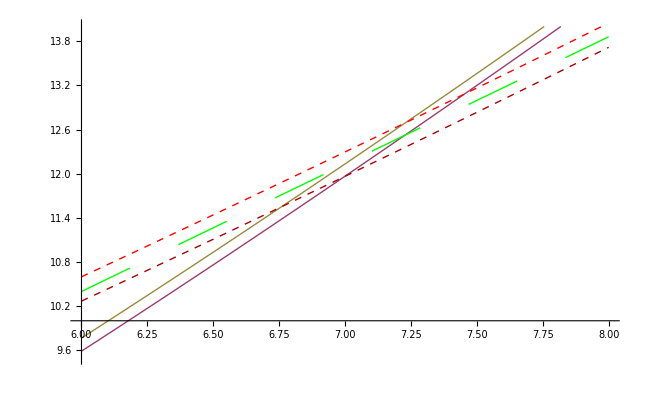

```mathematica
b = 0.2;
Plot[  {  Abs[  MM10r[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ],  
	Abs[  DD10r[  z[a, b],  1  ]   ],  Abs[  DD10r[  z[a, b],  -1  ]   ],
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 6, 8 },  PlotRange->{  9.5, 14  },
	PlotStyle->{  Thick, Thick, Thick,
				Directive[  Red, Dashed ],  Directive[ Darker[Red],  Dashed  ],
				Directive[  Green, Dashing[0.06]  ]  }  ]
```

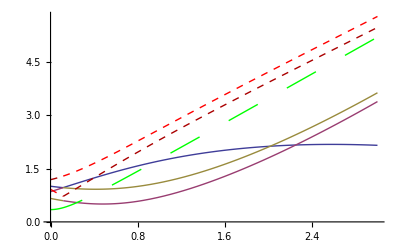

```mathematica
b = 0.2;
Plot[  {  Abs[  MM10r[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ],  
	Abs[  DD10r[  z[a, b],  1  ]   ],  Abs[  DD10r[  z[a, b],  -1  ]   ],
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 3  },  
	PlotStyle->{  Thick, Thick, Thick,
				Directive[  Red, Dashed ],  Directive[ Darker[Red],  Dashed  ],
				Directive[  Green, Dashing[0.06]  ]  }  ]
```

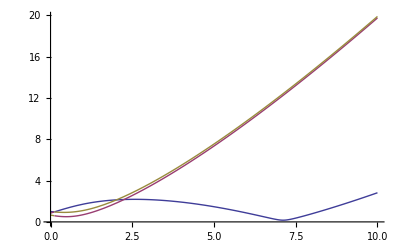

```mathematica
b = 0.2;
Plot[  {  Abs[  MM10r[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ]  },
	{  a, 0, 10 },  
	PlotStyle->{  Thick, Thick, Thick  }  ]
```

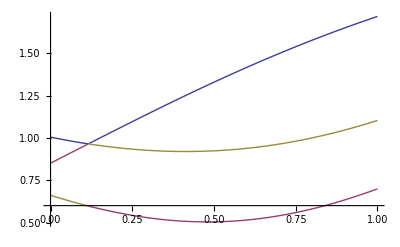

```mathematica
b = 0.2;
Plot[  {  Abs[  MM10r[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ],  Abs[  MM10r[  z[a, b]  ]  -  Q21[  z[a, b]  ]  ]  },
	{  a, 0, 1 },
	PlotStyle->{  Thick, Thick, Thick  }  ]
```

```mathematica
M10r[m_] :=   (  ⅇ^(2 π ⅈ / 3)  -  1  )W0[m]    +    ⅈ m0[m]

M21r[m_] := ⅇ^(2 π ⅈ /3) M10r[m]

M02r[m_]  := ⅇ^(2 π ⅈ /3) M21r[m]

D10r[m_, n_]  := M10r[m]   +   n Q10[m]

D21r[m_, n_]  := ⅇ^(2 π ⅈ /3) D10r[m, n]

D02r[m_, n_]  := ⅇ^(2 π ⅈ / 3)D21r[m, n]
```

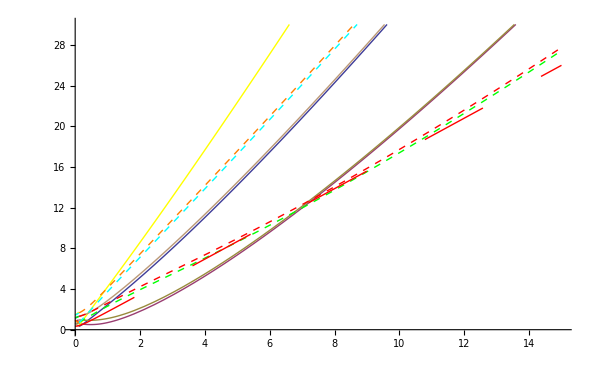

```mathematica
b = 0.2;
Plot[  {  Abs[  D10r[  z[a, b],  -1  ]  ],  Abs[  M10r[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  ],
	Abs[  D10r[  z[a, b], -2  ]  ], Abs[  D10r[  z[a, b],  2  ]  ],
	Abs[  D10r[  z[a, b],  1  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  -1  ]  +  Q20[  z[a, b]  ]  ],
	Abs[  D10r[  z[a,  b], 2  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  -2  ]  +  Q20[  z[a, b]  ]  ],
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 15 },  PlotRange->{  0, 30  },
	PlotStyle->{  Thick, Thick, Thick,
				Directive[  Yellow, Thick  ],  Directive[  Lighter[Brown],  Thick], 
				Directive[Dashed, Red], Directive[ Dashed, Green], 
				Directive[Dashed, Orange, Thick], Directive[Dashed, Cyan, Thick],
				Directive[Dashing[0.08], Red, Thin]  } ]
```

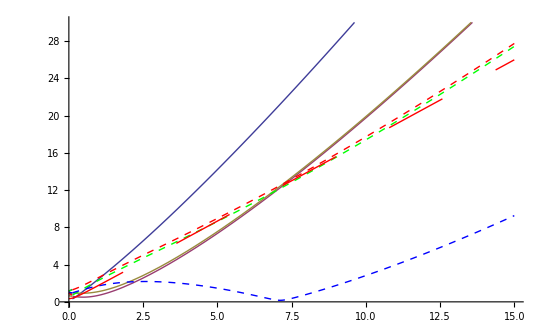

```mathematica
b = 0.2;
Plot[  {  Abs[  D10r[  z[a, b],  -1  ]  ],  Abs[  M10r[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  ],
	Abs[  D10r[  z[a, b],  -1  ]  +  Q20[  z[a, b]  ]  ],Abs[  M10r[  z[a, b]  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  +  Q20[  z[a, b]  ]  ],  
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 15 },  PlotRange->{  0, 30  },
	PlotStyle->{  Thick, Thick, Thick,
				Directive[ Dashed, Green], Directive[Dashed, Blue], Directive[Dashed, Red], 
				Directive[Dashing[0.08], Red, Thin]  } ]
```

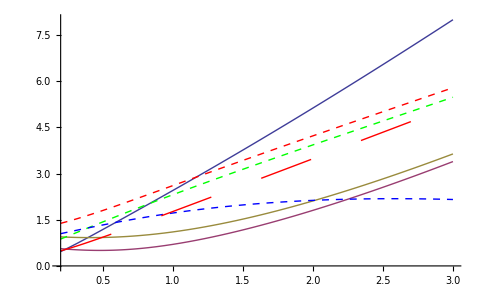

```mathematica
b = 0.2;
Plot[  {  Abs[  D10r[  z[a, b],  -1  ]  ],  Abs[  M10r[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  ],
	Abs[  D10r[  z[a, b],  -1  ]  +  Q20[  z[a, b]  ]  ],Abs[  M10r[  z[a, b]  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  +  Q20[  z[a, b]  ]  ],  
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, b, 3 },  
	PlotStyle->{  Thick, Thick, Thick,
				Directive[ Dashed, Green], Directive[Dashed, Blue], Directive[Dashed, Red], 
				Directive[Dashing[0.08], Red, Thin]  },
	AxesOrigin->{  b,  0  } ]
```

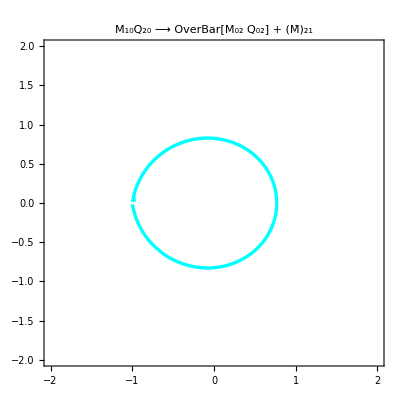

```mathematica
distance =2.0;
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrr[x, y]  ]    +    Q02[  mrr[x, y]  ]  ))/(-  ( M21r[  mrr[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_20  ⟶  OverBar[M_02 Q_02]  +  (M̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

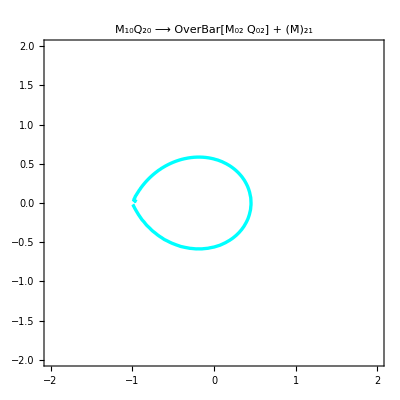

```mathematica
distance =2.0;
plotA = 
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrc[x, y]  ]    +    Q02[  mrc[x, y]  ]  ))/(-  ( M21r[  mrc[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_20  ⟶  OverBar[M_02 Q_02]  +  (M̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

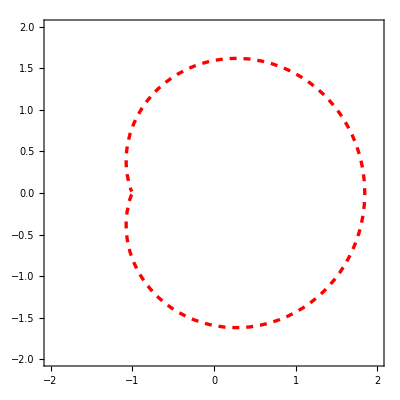

```mathematica
distance =2.0;
plotB = ContourPlot[   Evaluate[     {   Im[   M10r[  mrc[x,y]  ]/Q10[  mrc[x,y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006],    Red,    Dashed ] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

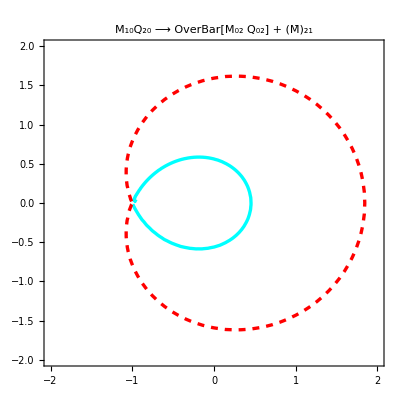

```mathematica
Show[  plotA, plotB  ]
```

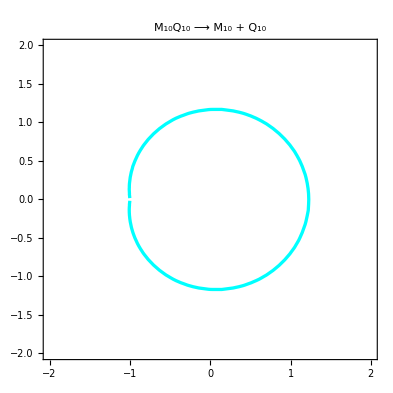

```mathematica
distance =2.0;
ContourPlot[   Evaluate[     {   Im[   M10u[mru[x,y]]/Q10[mru[x,y]]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_10  ⟶  M_10  +  Q_10",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

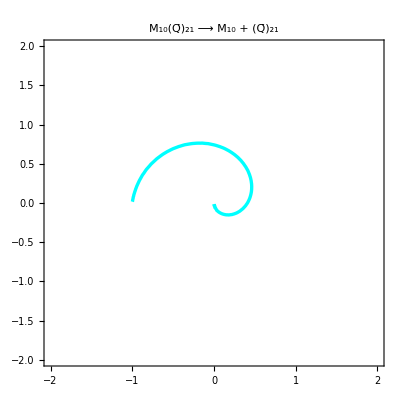

```mathematica
distance =2.0;
ContourPlot[   Evaluate[     {   Im[   M10u[mru[x,y]]/(- Q21[mru[x,y]])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10(Q̄)_21  ⟶  M_10  +  (Q̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

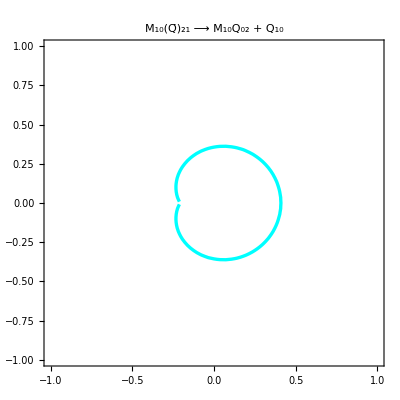

```mathematica
distance=1.0;
ContourPlot[   Evaluate[     {   Im[   (M10u[mru[x,y]]  +  Q02[mru[x,y]])/Q10[mru[x,y]]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10(Q̄)_21  ⟶  M_10Q_02  +  Q_10",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

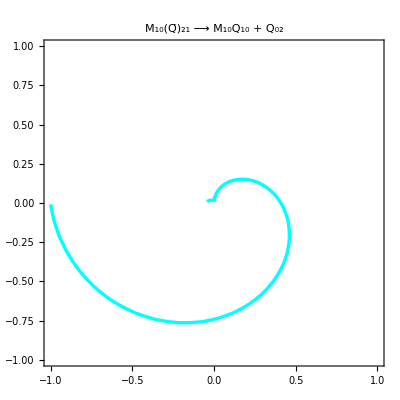

```mathematica
distance=1.0;
ContourPlot[   Evaluate[     {   Im[   (M10u[mru[x,y]]  +  Q10[mru[x,y]])/Q02[mru[x,y]]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10(Q̄)_21  ⟶  M_10Q_10  +  Q_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

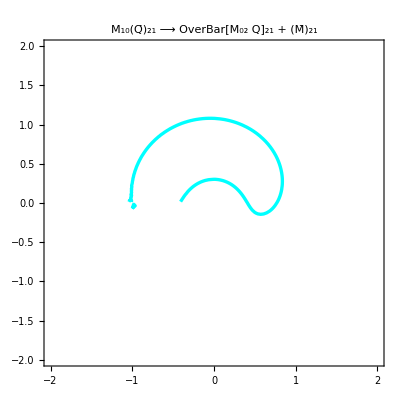

```mathematica
distance=2.0;
ContourPlot[   Evaluate[     {   Im[   (- ( M02u[mru[x,y]]  +  Q21[mru[x,y]] ))/(- M21u[mru[x,y]])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10(Q̄)_21  ⟶  OverBar[M_02 Q]_21  +  (M̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

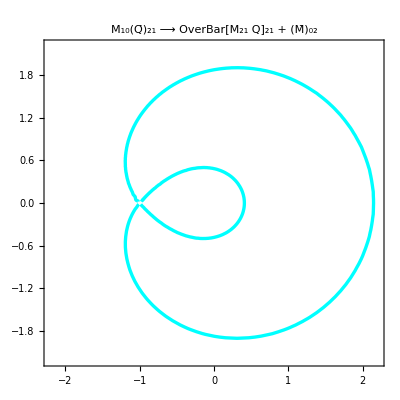

```mathematica
distance=2.2;
ContourPlot[   Evaluate[     {   Im[   (- ( M21u[mru[x,y]]  +  Q21[mru[x,y]] ))/(- M02u[mru[x,y]])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10(Q̄)_21  ⟶  OverBar[M_21 Q]_21  +  (M̄)_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

```mathematica
distance=0.2;
ContourPlot[   Evaluate[     {   Im[   (- M02u[mru[x,y]]  +  Q10[mru[x,y]])/(- M21u[mru[x,y]]  +  Q02[mru[x,y]])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10(Q̄)_21  ⟶  (M̄)_02Q_10  +  (M̄)_21Q_02
(all equal masses)",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

-Graphics-

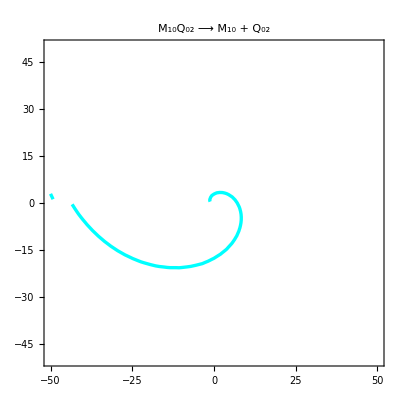

```mathematica
distance = 50.0;
ContourPlot[   Evaluate[     {   Im[   M10u[   mru[x, y]   ]/Q02[   mru[x, y]   ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_02  ⟶  M_10  +  Q_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

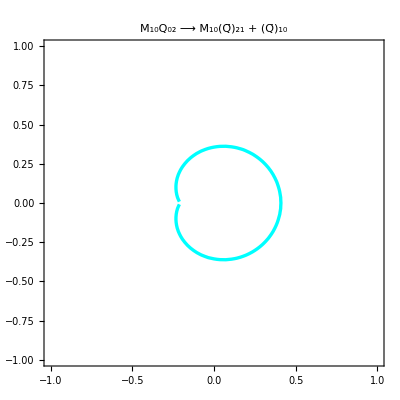

```mathematica
distance = 1.0;
ContourPlot[   Evaluate[     {   Im[   (M10u[   mru[x, y]   ]    -    Q21[    mru[x, y]    ])/(-  Q10[   mru[x, y]   ])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_02  ⟶  M_10(Q̄)_21  +  (Q̄)_10",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

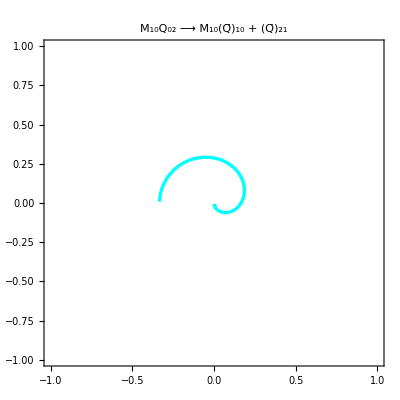

```mathematica
distance = 1.0;
ContourPlot[   Evaluate[     {   Im[   (M10u[   mru[x, y]   ]    -    Q10[    mru[x, y]    ])/(-  Q21[   mru[x, y]   ])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_02  ⟶  M_10(Q̄)_10  +  (Q̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

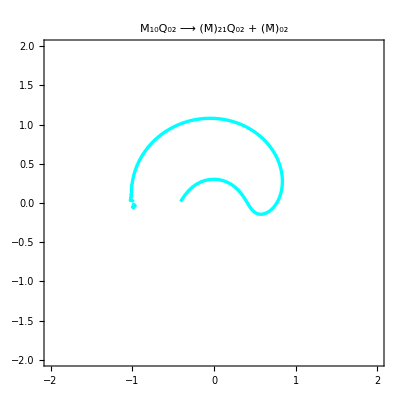

```mathematica
distance = 2.0;
ContourPlot[   Evaluate[     {   Im[   (-  M21u[   mru[x, y]   ]    +    Q02[    mru[x, y]    ])/(-  M02u[   mru[x, y]   ])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_02  ⟶  (M̄)_21Q_02  +  (M̄)_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

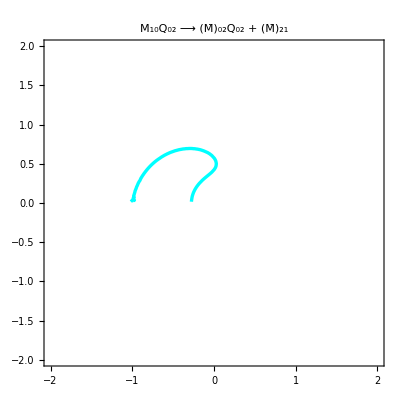

```mathematica
distance = 2.0;
ContourPlot[   Evaluate[     {   Im[   (-  M02u[   mru[x, y]   ]    +    Q02[    mru[x, y]    ])/(-  M21u[   mru[x, y]   ])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_02  ⟶  (M̄)_02Q_02  +  (M̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

```mathematica
distance=0.2;
ContourPlot[   Evaluate[     {   Im[   (-   (    M02u[mru[x,y]]  +  Q21[mru[x,y]]    ))/(-   (    M21u[mru[x,y]]  +  Q10[mru[x,y]]    ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_02  ⟶  (M̄)_02(Q̄)_21  +  (M̄)_21(Q̄)_10
(all equal masses)",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

-Graphics-

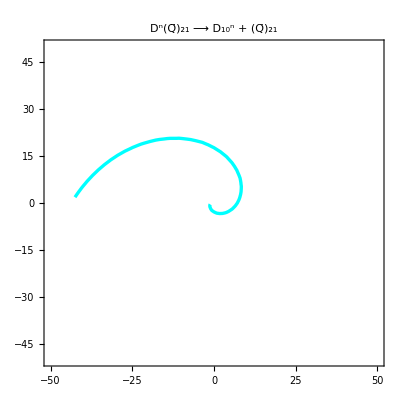

```mathematica
distance=50.0; n = 1;
ContourPlot[   Evaluate[     {   Im[   D10u[mru[x,y], n]/(- Q21[mru[x,y]])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D^n(Q̄)_21  ⟶  D_10^n  +  (Q̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

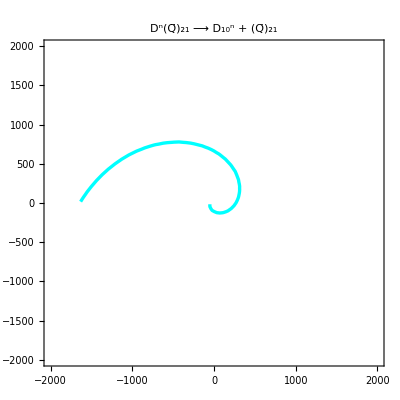

```mathematica
distance=2000.0; n = 2;
ContourPlot[   Evaluate[     {   Im[   D10u[mru[x,y], n]/(- Q21[mru[x,y]])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D^n(Q̄)_21  ⟶  D_10^n  +  (Q̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

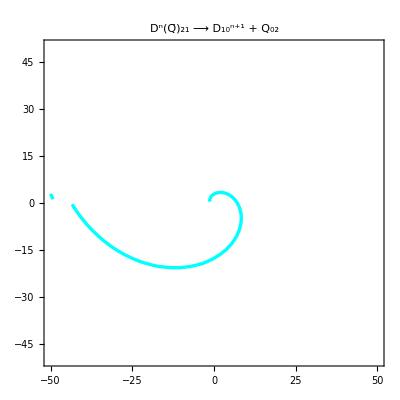

```mathematica
distance= 50.0; n = -1;
ContourPlot[   Evaluate[     {   Im[   D10u[mru[x,y], n+1]/Q02[mru[x,y]]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D^n(Q̄)_21  ⟶  D_10^(n+1)  +  Q_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

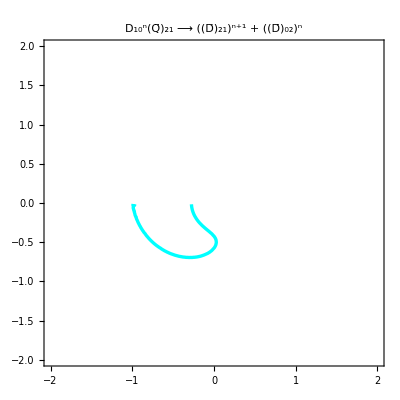

```mathematica
distance=2.0;     n = 1;
ContourPlot[   Evaluate[     {   Im[   (-     D21u[  mru[x, y], n + 1  ])/(-     D02u[  mru[x, y], n  ])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D_10^n(Q̄)_21  ⟶  ((D̄)_21)^(n+1)  +  ((D̄)_02)^n",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

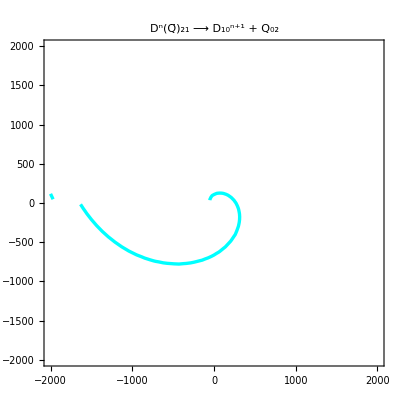

```mathematica
distance= 2000.0; n = -2;
ContourPlot[   Evaluate[     {   Im[   D10u[mru[x,y], n+1]/Q02[mru[x,y]]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {  Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D^n(Q̄)_21  ⟶  D_10^(n+1)  +  Q_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```